```mathematica
req=HTTPRequest["https://api.github.com/search/repositories?page="<>ToString[1]<>"&q=coronavirus",<|"Headers"->{"Authorization"->"token "<>token}|>]
```

HTTPRequest[…]

```mathematica
response=URLRead[req]
```

HTTPResponse[…]

```mathematica
ImportByteArray[response["BodyByteArray"],"RawJSON"]
```

```mathematica
i=1;
more=True;
result={};
While[more,
Pause[1];
Echo[i];
search=URLRead[HTTPRequest["https://api.github.com/search/repositories?page="<>ToString[i]<>"&q=coronavirus",<|"Headers"->{"Authorization"->"token "<>token}|>]];
json=ImportByteArray[search["BodyByteArray"],"RawJSON"];
Echo[Length[json]];
If[Length[json]=!=3,Abort[]];
AppendTo[result,json["items"]];
If[Length[json["items"]]>0,Null,more=False];
i++
];
```

1

3

2

3

3

3

4

3

5

3

6

3

7

3

8

3

9

3

10

3

11

3

12

3

13

3

14

3

```mathematica
14 30
```

420

```mathematica
420-30
```

390

```mathematica
Length[Flatten[result]]
```

386

```mathematica
ds=Dataset[Map[<|"name"->#["name"],"owner"->#["owner"]["login"]|>&,Flatten[result]]]
```

```mathematica
gettags[assoc_]:=Module[{repo,owner,url,tags},
repo=assoc["name"];
owner=assoc["owner"];
Echo[url=URL["https://api.github.com/repos/"<>owner<>"/"<>repo<>"/topics"]];
tags=URLRead[HTTPRequest[url,<|"Headers"->{"Accept"->"application/vnd.github.mercy-preview+json","Authorization"->"token "<>token}|>]];
tags=ImportByteArray[tags["BodyByteArray"],"RawJSON"];
<|"owner"->owner,"repo"->repo,"tags"->tags["names"]|>
]
```

```mathematica
Map[gettags,Take[ds,3]]
```

URL[https://api.github.com/repos/globalcitizen/2019-wuhan-coronavirus-data/topics]

URL[https://api.github.com/repos/nextstrain/ncov/topics]

URL[https://api.github.com/repos/GuangchuangYu/nCov2019/topics]

```mathematica
result2=Map[gettags,ds];
```

URL[https://api.github.com/repos/globalcitizen/2019-wuhan-coronavirus-data/topics]

URL[https://api.github.com/repos/nextstrain/ncov/topics]

URL[https://api.github.com/repos/GuangchuangYu/nCov2019/topics]

URL[https://api.github.com/repos/2019ncovmemory/nCovMemory/topics]

URL[https://api.github.com/repos/JohnCoene/coronavirus/topics]

URL[https://api.github.com/repos/839Studio/Novel-Coronavirus-Updates/topics]

URL[https://api.github.com/repos/ncovis/choropleth/topics]

URL[https://api.github.com/repos/sorxrob/2019-ncov-frontend/topics]

URL[https://api.github.com/repos/docligot/coronatracker-analytics/topics]

URL[https://api.github.com/repos/YiranJing/Coronavirus-Epidemic-2019-nCov/topics]

URL[https://api.github.com/repos/AaronWard/coronavirus-analysis/topics]

URL[https://api.github.com/repos/hysios/coronavirus/topics]

URL[https://api.github.com/repos/lbj96347/2020-new-coronavirus-live-map/topics]

URL[https://api.github.com/repos/sorxrob/2019-ncov-api/topics]

URL[https://api.github.com/repos/chrism0dwk/wuhan/topics]

URL[https://api.github.com/repos/dreamerjackson/coronavirus/topics]

URL[https://api.github.com/repos/HopkinsIDD/ncov_incubation/topics]

URL[https://api.github.com/repos/widscommunityorg/CoronaV_Challenge/topics]

URL[https://api.github.com/repos/artic-network/artic-ncov2019/topics]

URL[https://api.github.com/repos/vilaca/wuhan-coronavirus-outbreak/topics]

URL[https://api.github.com/repos/antonlukin/2019-nCoV/topics]

URL[https://api.github.com/repos/LiveCoronaDetector/livecod/topics]

URL[https://api.github.com/repos/kaichih/CoronavirusChart/topics]

URL[https://api.github.com/repos/WebDevSimplified/Coronavirus-Chrome-Extension/topics]

URL[https://api.github.com/repos/pdtyreus/coronavirus-ds/topics]

URL[https://api.github.com/repos/alext234/coronavirus-stats/topics]

URL[https://api.github.com/repos/MeoncStudio/Anti_2019-ncoV/topics]

URL[https://api.github.com/repos/DnCov/transparent-info/topics]

URL[https://api.github.com/repos/iidx/corona-tracker/topics]

URL[https://api.github.com/repos/WeileiZeng/red-cross/topics]

URL[https://api.github.com/repos/nextstrain/cov/topics]

URL[https://api.github.com/repos/Xetera/corona/topics]

URL[https://api.github.com/repos/arnoudbuzing/wolfram-coronavirus/topics]

URL[https://api.github.com/repos/etchorigin/ncov2019/topics]

URL[https://api.github.com/repos/coddec/2020-new-coronavirus/topics]

URL[https://api.github.com/repos/instafluff/Coronavirus/topics]

URL[https://api.github.com/repos/ChengF-Lab/2019-nCoV/topics]

URL[https://api.github.com/repos/avischiffmann/Coronavirus-Dashboard/topics]

URL[https://api.github.com/repos/WuhanZhuRong/DonationChannel/topics]

URL[https://api.github.com/repos/Laeyoung/Wuhan-Coronavirus-API/topics]

URL[https://api.github.com/repos/aitahtman/coronavirus/topics]

URL[https://api.github.com/repos/Kyald1412/CoronaVirus-2019-nCoV-Live-Tracking/topics]

URL[https://api.github.com/repos/sagunsh/corona-live/topics]

URL[https://api.github.com/repos/jarekpelczynski/ncov-data-fetcher/topics]

URL[https://api.github.com/repos/the-robot/corona-bot/topics]

URL[https://api.github.com/repos/jianxu305/nCov2019_analysis/topics]

URL[https://api.github.com/repos/JordanMicahBennett/SMART-CORONA_VIRUS_DETECTOR/topics]

URL[https://api.github.com/repos/sijiali57/coronavirus_data/topics]

URL[https://api.github.com/repos/kevinlu1248/corona/topics]

URL[https://api.github.com/repos/yitao94/2019-nCoV/topics]

URL[https://api.github.com/repos/xcv58/Coronavirus/topics]

URL[https://api.github.com/repos/labsletemps/coronavirus-world-map/topics]

URL[https://api.github.com/repos/JunjieZhouwust/Coronavirus-Estimation/topics]

URL[https://api.github.com/repos/bjwa2020/coronavirus/topics]

URL[https://api.github.com/repos/fangohr/coronavirus-2020/topics]

URL[https://api.github.com/repos/Sviper-07/CoronavirusOdesseyRepo/topics]

URL[https://api.github.com/repos/muditham90/viral-coronavirus/topics]

URL[https://api.github.com/repos/ugovaretto/corona/topics]

URL[https://api.github.com/repos/iPomme/GameJame2020/topics]

URL[https://api.github.com/repos/kaiyz/corona/topics]

URL[https://api.github.com/repos/jairoD/coronavirus-api/topics]

URL[https://api.github.com/repos/Cyberist-Edgar/2020-novel-coronavirus/topics]

URL[https://api.github.com/repos/mshyun/coronavirus/topics]

URL[https://api.github.com/repos/mcodz/coronavirus/topics]

URL[https://api.github.com/repos/netqyq/coronavirus-stat/topics]

URL[https://api.github.com/repos/mudiant/viral-coronavirus/topics]

URL[https://api.github.com/repos/Coronavirus2019/Coronavirus-2019/topics]

URL[https://api.github.com/repos/jairoD/coronavirus/topics]

URL[https://api.github.com/repos/lbj96347/2020-new-coronavirus-info-crawler/topics]

URL[https://api.github.com/repos/ivan-iliev/mc-2d/topics]

URL[https://api.github.com/repos/burgess/2019-nCoV/topics]

URL[https://api.github.com/repos/lina/lina.github.io/topics]

URL[https://api.github.com/repos/stephan227/coronavirus-data-hq/topics]

URL[https://api.github.com/repos/chunyeow/dash-coronavirus/topics]

URL[https://api.github.com/repos/joshuaferr1s/coronavirus/topics]

URL[https://api.github.com/repos/iuming/Coronavirus/topics]

URL[https://api.github.com/repos/POGE0124/Coronavirus_quantity_prediction/topics]

URL[https://api.github.com/repos/XuCQ/WuhanCoronavirusDataCrawel/topics]

URL[https://api.github.com/repos/filswa/coronavirusapi/topics]

URL[https://api.github.com/repos/openthings/2020ncov/topics]

URL[https://api.github.com/repos/dranoer/corona/topics]

URL[https://api.github.com/repos/SpencerAung/coronavirus-info/topics]

URL[https://api.github.com/repos/ddong63/coronavirus_analysis/topics]

URL[https://api.github.com/repos/kealyn/Wuhan2019/topics]

URL[https://api.github.com/repos/MCN-TV-NEWS/EDITOR/topics]

URL[https://api.github.com/repos/ExtReMLapin/gmod_coronavirus/topics]

URL[https://api.github.com/repos/ricosmall/2019-ncov/topics]

URL[https://api.github.com/repos/htso/Coronavirus_Epidemic/topics]

URL[https://api.github.com/repos/biomedontology/cido/topics]

URL[https://api.github.com/repos/feraliscatus/VxAfee/topics]

URL[https://api.github.com/repos/piscium2010/coronavirus-map/topics]

URL[https://api.github.com/repos/aknow2/situation-coronavirus/topics]

URL[https://api.github.com/repos/epiforecasts/WuhanSeedingVsTransmission/topics]

URL[https://api.github.com/repos/dakula009/China_CoronaVirus_Data_Miner/topics]

URL[https://api.github.com/repos/EveDong/2019-nCoV/topics]

URL[https://api.github.com/repos/ddlan/corona-oh-na-na/topics]

URL[https://api.github.com/repos/kianweelee/Data-Visualisation--Coronavirus-confirmed-cases/topics]

URL[https://api.github.com/repos/eragmus/2019ncov/topics]

URL[https://api.github.com/repos/henryshw/VirusTracker/topics]

URL[https://api.github.com/repos/JenQian/coronavirus-data-ETL/topics]

URL[https://api.github.com/repos/yx-z/wuhan/topics]

URL[https://api.github.com/repos/AndyLPK247/coronavirus-scraper/topics]

URL[https://api.github.com/repos/SuperDiscovery/NCP-Model/topics]

URL[https://api.github.com/repos/itsyaoyu/wuhan_coronavirus/topics]

URL[https://api.github.com/repos/sanghy/epidemicsituation2020/topics]

URL[https://api.github.com/repos/QMHTMY/Coronavirus/topics]

URL[https://api.github.com/repos/audreyqyfu/wuhancov/topics]

URL[https://api.github.com/repos/RuyiLi/coronatracker/topics]

URL[https://api.github.com/repos/KezhiLi/Wuhan_Coronavirus/topics]

URL[https://api.github.com/repos/martinedoesgis/novel-coronavirus/topics]

URL[https://api.github.com/repos/ergodiclife/wuhan-coronavirus/topics]

URL[https://api.github.com/repos/ShuuTsubaki/Wuhan-Coronavirus-Even-Timeline/topics]

URL[https://api.github.com/repos/ljnicol/coronavirus_viz/topics]

URL[https://api.github.com/repos/MaBeuLux88/coronavirus-mongodb/topics]

URL[https://api.github.com/repos/aliciawyy/coronavirus-outbreak-log/topics]

URL[https://api.github.com/repos/EricLiam94/VirusVisual/topics]

URL[https://api.github.com/repos/zipengliu/ncov-vis-wuhan2020/topics]

URL[https://api.github.com/repos/perlatex/2019-nCoV/topics]

URL[https://api.github.com/repos/liu-zoe/wuhancv/topics]

URL[https://api.github.com/repos/sdwfrost/mers-analysis/topics]

URL[https://api.github.com/repos/839-Studio/Noval-Coronavirus-763-Cases/topics]

URL[https://api.github.com/repos/lukas-jue/coronavirus/topics]

URL[https://api.github.com/repos/donpaul999/coronavirusMap/topics]

URL[https://api.github.com/repos/sgfm/CoronavirusVisualization/topics]

URL[https://api.github.com/repos/SuriousCompany/CoronavirusObserver/topics]

URL[https://api.github.com/repos/reetaa/coronavirus2020/topics]

URL[https://api.github.com/repos/yuhanbae06/coronavirus/topics]

URL[https://api.github.com/repos/blowsys/Coronavirus/topics]

URL[https://api.github.com/repos/kaixin1976/coronavirus/topics]

URL[https://api.github.com/repos/ykl124/Shanghai2020/topics]

URL[https://api.github.com/repos/xstarseed/coronavirus/topics]

URL[https://api.github.com/repos/elvinaqa/The-Rise-of-CoronaVirus/topics]

URL[https://api.github.com/repos/hriewe/CoronavirusTracker/topics]

URL[https://api.github.com/repos/JackJoeng/coronavirus/topics]

URL[https://api.github.com/repos/choderalab/coronavirus/topics]

URL[https://api.github.com/repos/divyeshj02/CoronavirusDetection/topics]

URL[https://api.github.com/repos/bahe007/CoronaTracker/topics]

URL[https://api.github.com/repos/FrankChen021/2019-ncov/topics]

URL[https://api.github.com/repos/qingzma/coronavirusMonitor/topics]

URL[https://api.github.com/repos/jubayer-hossain/CoronavirusTracking/topics]

URL[https://api.github.com/repos/cooerson/2019-nCoV/topics]

URL[https://api.github.com/repos/apex-stack/true-coronavirus/topics]

URL[https://api.github.com/repos/SuperSt3ve/coronavirus/topics]

URL[https://api.github.com/repos/TheGodOfHuaji/Coronavirus/topics]

URL[https://api.github.com/repos/Dork3yyyy/coronavirus/topics]

URL[https://api.github.com/repos/joaogrosso/Coronavirus/topics]

URL[https://api.github.com/repos/mot200286mot/CoronaVirus/topics]

URL[https://api.github.com/repos/flyffast/CoronavirusHackUCI/topics]

URL[https://api.github.com/repos/bovinemagnet/coronavirus-neo4j/topics]

URL[https://api.github.com/repos/casperbrike/corona_bot/topics]

URL[https://api.github.com/repos/kalzeo/nCoV-API/topics]

URL[https://api.github.com/repos/bwanglzu/404-not-found/topics]

URL[https://api.github.com/repos/lprone/coronavirus/topics]

URL[https://api.github.com/repos/finateautomata/Coronavirus/topics]

URL[https://api.github.com/repos/ozpv/Coronavirus/topics]

URL[https://api.github.com/repos/itoic/coronavirus/topics]

URL[https://api.github.com/repos/toyourheart163/coronavirus/topics]

URL[https://api.github.com/repos/sta199-sp20-002/appex-04-coronavirus/topics]

URL[https://api.github.com/repos/dizzySummer/coronavirusRealTimeData/topics]

URL[https://api.github.com/repos/TheCode-Jedi/CoronaVirus-MD/topics]

URL[https://api.github.com/repos/DnCov/DnCov/topics]

URL[https://api.github.com/repos/notfree/Coronavirus/topics]

URL[https://api.github.com/repos/Schukerz/Coronavirus/topics]

URL[https://api.github.com/repos/nurulc/coronavirus/topics]

URL[https://api.github.com/repos/dirkarnez/mask/topics]

URL[https://api.github.com/repos/PengKuang/wuhan2020-oversea/topics]

URL[https://api.github.com/repos/PranavPable/2019-n-CoV-Virus-Dashboard/topics]

URL[https://api.github.com/repos/liuyangly25/infection_prediction/topics]

URL[https://api.github.com/repos/ncoronavirus/Toronto2020/topics]

URL[https://api.github.com/repos/donghoony1/2019-nCoV/topics]

URL[https://api.github.com/repos/Nrg800/NCov2019_Data/topics]

URL[https://api.github.com/repos/EthanGeekFan/nCoV/topics]

URL[https://api.github.com/repos/WooilJeong/novel_coronavirus/topics]

URL[https://api.github.com/repos/JakeJing/wuhan-coronavirus/topics]

URL[https://api.github.com/repos/CoDeRgAnEsh/nCoV-2019/topics]

URL[https://api.github.com/repos/changbing2019/lstm4ncor/topics]

URL[https://api.github.com/repos/chunyeow/coronavirus-crawling/topics]

URL[https://api.github.com/repos/sungml92/2019-nCov/topics]

URL[https://api.github.com/repos/kidanh/coronavirus/topics]

URL[https://api.github.com/repos/zk213/Coronavirus/topics]

URL[https://api.github.com/repos/KimOlsson/coronavirus-project/topics]

URL[https://api.github.com/repos/ThinkGeo/Coronavirus-Wuhan-nCoV-2019/topics]

URL[https://api.github.com/repos/nyem69/coronavirus_dashboard/topics]

URL[https://api.github.com/repos/nickofc/coronavirus/topics]

URL[https://api.github.com/repos/teddylun/coronavirus/topics]

URL[https://api.github.com/repos/alamjane/Coronavirus/topics]

URL[https://api.github.com/repos/Zhnan811/coronavirus/topics]

URL[https://api.github.com/repos/leonluleonlu/2019-nCoV_Donation/topics]

URL[https://api.github.com/repos/eebrown/data2019nCoV/topics]

URL[https://api.github.com/repos/CSSEGISandData/2019-nCoV/topics]

URL[https://api.github.com/repos/kalzeo/CoronavirusWebsiteTracker/topics]

URL[https://api.github.com/repos/chenhua1008/CoronavirusPersonalReport/topics]

URL[https://api.github.com/repos/yarfer/coronavirus/topics]

URL[https://api.github.com/repos/GHumorBS/Coronavirus/topics]

URL[https://api.github.com/repos/Yuriyama/Coronavirus/topics]

URL[https://api.github.com/repos/rnjsalswl93/Coronavirus/topics]

URL[https://api.github.com/repos/johnmelodyme/CoronaVirus/topics]

URL[https://api.github.com/repos/themarcusaurelius/coronaVirus/topics]

URL[https://api.github.com/repos/DuongThuyet/coronaVirus/topics]

URL[https://api.github.com/repos/MarGonz7/coronavirus/topics]

URL[https://api.github.com/repos/juwikuang/coronavirus/topics]

URL[https://api.github.com/repos/igorisolomon/coronavirus/topics]

URL[https://api.github.com/repos/cfshi/coronavirus/topics]

URL[https://api.github.com/repos/colortail/coronavirus/topics]

URL[https://api.github.com/repos/Dajnowicz/CoronaVirus/topics]

URL[https://api.github.com/repos/HardWorkerIlya/coronavirus/topics]

URL[https://api.github.com/repos/NarekSag/CoronaVirus/topics]

URL[https://api.github.com/repos/741wcai/coronavirus/topics]

URL[https://api.github.com/repos/diehard04/coronavirus/topics]

URL[https://api.github.com/repos/henry123i/coronavirus/topics]

URL[https://api.github.com/repos/escudero/coronavirus/topics]

URL[https://api.github.com/repos/Ruchit007/CoronaVirus/topics]

URL[https://api.github.com/repos/guptaekarigar/coronavirustracker/topics]

URL[https://api.github.com/repos/Koohoko/Coronavirus_Bayseian_Modelling/topics]

URL[https://api.github.com/repos/davy868/propagation-model-for-2019-nCov/topics]

URL[https://api.github.com/repos/damonYuan/ncov-api-k8s/topics]

URL[https://api.github.com/repos/hernanmd/nCoV-2019/topics]

URL[https://api.github.com/repos/aejsong/novel-coronavirus-exploratory-analysis/topics]

URL[https://api.github.com/repos/daniel2231/coronavirusmap/topics]

URL[https://api.github.com/repos/Gazerbeamco/coronavirus/topics]

URL[https://api.github.com/repos/karolkolodziej/coronavirus/topics]

URL[https://api.github.com/repos/143034/-coronavirus-/topics]

URL[https://api.github.com/repos/PratirupG/coronavirusanalysis/topics]

URL[https://api.github.com/repos/nerocui/coronavirustracker/topics]

URL[https://api.github.com/repos/larsgimse/coronaviruslamp/topics]

URL[https://api.github.com/repos/jwktls/Coronavirus_ios/topics]

URL[https://api.github.com/repos/ctedijanto/coronavirus-seasonality/topics]

URL[https://api.github.com/repos/mrmattwright-inc/coronavirus-virus/topics]

URL[https://api.github.com/repos/optoisolated/coronavirus-stats/topics]

URL[https://api.github.com/repos/quangvo09/coronavirus_crawler/topics]

URL[https://api.github.com/repos/geunm/Coronavirus-macro/topics]

URL[https://api.github.com/repos/joshualeung/wuhan-coronavirus/topics]

URL[https://api.github.com/repos/maksim72/coronavirus-website/topics]

URL[https://api.github.com/repos/A-Yifeng/wuhan-coronavirus/topics]

URL[https://api.github.com/repos/Olivine-Ryo/coronavirus_map/topics]

URL[https://api.github.com/repos/imsoncod/Coronavirus-Map/topics]

URL[https://api.github.com/repos/epignatelli/coronavirus-infographics/topics]

URL[https://api.github.com/repos/JILI1028/Wuhan-Coronavirus/topics]

URL[https://api.github.com/repos/pavel-ilin/coronavirus-map/topics]

URL[https://api.github.com/repos/android-apps-apk/coronavirus-protect/topics]

URL[https://api.github.com/repos/abuuzayr/coronavirus-apps/topics]

URL[https://api.github.com/repos/fasalmbt/corona-virus-data-tracker/topics]

URL[https://api.github.com/repos/developers-arm/Coronavirus-things/topics]

URL[https://api.github.com/repos/HesterLim/coronavirus-analysis/topics]

URL[https://api.github.com/repos/smorfopoulou/coronavirus_genbank/topics]

URL[https://api.github.com/repos/andrewadiletta/coronavirus_gizmo/topics]

URL[https://api.github.com/repos/JonathanJing/China-Coronavirus/topics]

URL[https://api.github.com/repos/SamuelePolimi/Coronavirus-Report/topics]

URL[https://api.github.com/repos/PatornJantara/coronavirus-detection/topics]

URL[https://api.github.com/repos/samjakobcavazos/Coronavirus-Tracker/topics]

URL[https://api.github.com/repos/victormaggie/coronavirus-research/topics]

URL[https://api.github.com/repos/kobkrit/data-coronavirus/topics]

URL[https://api.github.com/repos/lingye0926/china_coronavirus/topics]

URL[https://api.github.com/repos/shadowkiller162/WuhanCoronavirus/topics]

URL[https://api.github.com/repos/L0per/wuhan-coronavirus/topics]

URL[https://api.github.com/repos/catofsof/coronavirus-api/topics]

URL[https://api.github.com/repos/Sun2yKid/Anti-2019-nCoV/topics]

URL[https://api.github.com/repos/neotan/wuhan-coronavirus-crawler-nodejs/topics]

URL[https://api.github.com/repos/gson2019/WuhanPneumonia/topics]

URL[https://api.github.com/repos/yixinshi/coronavirus-map/topics]

URL[https://api.github.com/repos/Vijayb023/CoronaVirus-/topics]

URL[https://api.github.com/repos/samrahimi/coronavirus-api/topics]

URL[https://api.github.com/repos/jwktls/Coronavirus_android/topics]

URL[https://api.github.com/repos/vndevpro/2019-ncov-confirmed/topics]

URL[https://api.github.com/repos/louisnot/n-Cov2019/topics]

URL[https://api.github.com/repos/WeileiZeng/OpenSourceWuhan/topics]

URL[https://api.github.com/repos/nnikniL/2019-nCoV_Notes/topics]

URL[https://api.github.com/repos/asmointernational123/coronavirus-blog/topics]

URL[https://api.github.com/repos/Zeldsc/coronavirus_analises/topics]

URL[https://api.github.com/repos/ddzyan/new-coronavirus/topics]

URL[https://api.github.com/repos/nyem69/coronavirus_data/topics]

URL[https://api.github.com/repos/cyrusxzw/wuhan-coronavirus/topics]

URL[https://api.github.com/repos/tomsharp/coronavirus-dashboard/topics]

URL[https://api.github.com/repos/Daggron/No-coronavirus/topics]

URL[https://api.github.com/repos/EnderRL/wuhan/topics]

URL[https://api.github.com/repos/zire/pandemic2020/topics]

URL[https://api.github.com/repos/tangingw/coronavirus_scrapper/topics]

URL[https://api.github.com/repos/PrabhaSahiti/Coronavirus_spread/topics]

URL[https://api.github.com/repos/yc111/coronavirus-map/topics]

URL[https://api.github.com/repos/dexterwah/coronavirus-news/topics]

URL[https://api.github.com/repos/Felix-lxd/coronavirus-map/topics]

URL[https://api.github.com/repos/ZhanweiDU/2019nCov/topics]

URL[https://api.github.com/repos/jdrakephd/wuhan-stochastic-model/topics]

URL[https://api.github.com/repos/lichader/coronavirus-bot/topics]

URL[https://api.github.com/repos/yongjun21/wuhan-coronavirus/topics]

URL[https://api.github.com/repos/ExpDev07/coronavirus-tracker/topics]

URL[https://api.github.com/repos/green-trees/novel-coronavirus/topics]

URL[https://api.github.com/repos/thiennv2896/Corona-Monitor/topics]

URL[https://api.github.com/repos/edwardcooper/wuhan-virus-paper/topics]

URL[https://api.github.com/repos/changbing2019/LSTM4Coronavirusprediction/topics]

URL[https://api.github.com/repos/GloryWong/2019ncov-xiaogan/topics]

URL[https://api.github.com/repos/SauravSanjay/Data-Science-Coronavirus/topics]

URL[https://api.github.com/repos/johnjaiharjose/CoronaVirusMapper/topics]

URL[https://api.github.com/repos/imanpalsingh/coronavirus-data-analysis/topics]

URL[https://api.github.com/repos/Pyxisq/CoronaVirusSpread/topics]

URL[https://api.github.com/repos/craftsman-lab/x-coronavirus-volunteer/topics]

URL[https://api.github.com/repos/Fjallen/Coronavirus-Analysis/topics]

URL[https://api.github.com/repos/rbrick/corona-tracker/topics]

URL[https://api.github.com/repos/ExpDev07/coronavirus-tracker-api/topics]

URL[https://api.github.com/repos/diy2learn/conronavirus_viz/topics]

URL[https://api.github.com/repos/jonklaric/CoronaVirusModel/topics]

URL[https://api.github.com/repos/anevaluator/ncov-analysis/topics]

URL[https://api.github.com/repos/thegostisdead/CoronaVirus-Vizualizer/topics]

URL[https://api.github.com/repos/x-craftsman/x-coronavirus-bee/topics]

URL[https://api.github.com/repos/lumaaaaaa/KoronaCS/topics]

URL[https://api.github.com/repos/Bohan-S/Coronavirus-Analysis/topics]

URL[https://api.github.com/repos/renyi/coronavirus_scrapper/topics]

URL[https://api.github.com/repos/yuejoo/Coronavirus-Wuhan-101/topics]

URL[https://api.github.com/repos/PrawiraGenestonlia/anti-coronavirus-backend/topics]

URL[https://api.github.com/repos/dankaki/wuhan_coronavirus_risk/topics]

URL[https://api.github.com/repos/easonlai/Visualization_for_Wuhan-Coronavirus_2019-nCov_cases_HK/topics]

URL[https://api.github.com/repos/mame0521/2019-nCoV-/topics]

URL[https://api.github.com/repos/garchingastronomy/-/topics]

URL[https://api.github.com/repos/CalBearKen/WuhanCoronaVirusMutationMonitoring/topics]

URL[https://api.github.com/repos/suhanlee/rn-coronavirus-info/topics]

URL[https://api.github.com/repos/bhuwanesh340/Coronavirus_Tweets_Analysis/topics]

URL[https://api.github.com/repos/weiaiwayne/Coronavirus_on_Twitter/topics]

URL[https://api.github.com/repos/h-mehta/Wuhan-Coronavirus-Visualization/topics]

URL[https://api.github.com/repos/x-craftsman/x-coronavirus-fee/topics]

URL[https://api.github.com/repos/williamli/coronavirus-home-quarantine-hk/topics]

URL[https://api.github.com/repos/realvivekganta/CoronaVirusTweetScraper/topics]

URL[https://api.github.com/repos/Cricetulus/wuhan-coronavirus-prediction-/topics]

URL[https://api.github.com/repos/dotis90/coronavirus-block-chrome-extension/topics]

URL[https://api.github.com/repos/msyazwan/news_coronavirus_json/topics]

URL[https://api.github.com/repos/craftsman-lab/x-coronavirus-apis/topics]

URL[https://api.github.com/repos/peirangxu/Project_2_Coronavirus_-Pneumonia/topics]

URL[https://api.github.com/repos/craftsman-lab/x-coronavirus-hospital/topics]

URL[https://api.github.com/repos/OBMGIS/CoronaVirusMap/topics]

URL[https://api.github.com/repos/Formalin564/2019-Novel-Coronavirus/topics]

URL[https://api.github.com/repos/presstofan/2019-nCov-data-collection/topics]

URL[https://api.github.com/repos/CoryAndrewHofstad/Shanghai-During-and-After-Bastyr-Landing-CoronaVirus-Source-/topics]

URL[https://api.github.com/repos/AlaaSenjab/coronavirus_live_map/topics]

URL[https://api.github.com/repos/odaiwai/2020_wuhan_coronavirus/topics]

URL[https://api.github.com/repos/guardian/interactive-coronavirus-tracker-map/topics]

URL[https://api.github.com/repos/yangmingleiSYSU/2019-novel-coronavirus/topics]

URL[https://api.github.com/repos/UW-CSE442-WI20/A3-coronavirus-alert/topics]

URL[https://api.github.com/repos/tunguyen2504/coronavirus-tracking-app/topics]

URL[https://api.github.com/repos/thecatgamer137/Joke.Win32.Coronavirus/topics]

URL[https://api.github.com/repos/hwei/AntiCoronavirus2/topics]

URL[https://api.github.com/repos/muniah/2019-Novel-Coronavirus-analysis/topics]

URL[https://api.github.com/repos/juliuswuwu/Coronavirus-data-visalization-project/topics]

URL[https://api.github.com/repos/stephan227/coronavirus-data-hq-api/topics]

URL[https://api.github.com/repos/ygmpkk/coronavirus-map-backend/topics]

URL[https://api.github.com/repos/yuwei1985/2020WuhanCoronavirus/topics]

URL[https://api.github.com/repos/kalzeo/CoronaVirusTracker/topics]

URL[https://api.github.com/repos/RaSt92/coronavirus-chrome-extension/topics]

URL[https://api.github.com/repos/Up-s/CoronaVirusServiceCenter/topics]

URL[https://api.github.com/repos/perell2014/2019-wuhan-coronavirus-data/topics]

URL[https://api.github.com/repos/HwdTech010/CoronaVirusMaleware/topics]

URL[https://api.github.com/repos/iam-abbas/Coronavirus-Data-Visualization/topics]

URL[https://api.github.com/repos/ciszakdamian/Coronavirus-2019-ncov-Predictions-ML/topics]

URL[https://api.github.com/repos/Jinchili/wuhan_2019_coronavirus_model_navigate/topics]

URL[https://api.github.com/repos/guardian/interactive-coronavirus-tracker-asia-map/topics]

URL[https://api.github.com/repos/gadm21/CoronaVirus-spread-prediction-model/topics]

URL[https://api.github.com/repos/initiumdev/20200203-international-novel-coronavirus-live/topics]

URL[https://api.github.com/repos/samrahimi/samrahimi.github.io/topics]

URL[https://api.github.com/repos/Vicky0528/Project2-WuHan-Coronavirus/topics]

URL[https://api.github.com/repos/DarlingHang/CSAPP_labs/topics]

URL[https://api.github.com/repos/duiyu/get-out-game/topics]

URL[https://api.github.com/repos/jenzushsu/powerbi-ncov2019/topics]

URL[https://api.github.com/repos/samrahimi/daily-corona/topics]

URL[https://api.github.com/repos/standwithwuhan/rumorsbreaker/topics]

URL[https://api.github.com/repos/Vopaaz/nCov-transportation-subscriber/topics]

URL[https://api.github.com/repos/lumaaaaaa/Korona/topics]

URL[https://api.github.com/repos/qingweihk/New-coronavirus-development-trend-Feb-6/topics]

URL[https://api.github.com/repos/Nova-Xue/Days-In-China-with-Coronavirus-Spreading/topics]

URL[https://api.github.com/repos/balandhanka/coronavirus-infectent-prediction-using-linear-regression-model/topics]

URL[https://api.github.com/repos/gustavocarmoh/Analise-Corona-Virus/topics]

URL[https://api.github.com/repos/viral-coronavirus-dev/static-website/topics]

URL[https://api.github.com/repos/BrunoCdot/Actualizaciones-Coronavirus-2019-nCoV-Gobierno-de-Espana/topics]

URL[https://api.github.com/repos/aasgary/-Novel-Coronavirus-2019-nCoV-Outbreake-Timelapse/topics]

URL[https://api.github.com/repos/viral-coronavirus-dev/alert-app/topics]

URL[https://api.github.com/repos/CoryAndrewHofstad/SOURCE-OF-CORONAVIRUS-OUTBREAK-BOSC23-HUMAN-LABORATORY-SLAVES/topics]

URL[https://api.github.com/repos/BrunoCdot/PROCEDIMIENTO-DE-ACTUACION-2019-nCoV-/topics]

URL[https://api.github.com/repos/akalia25/StockMarket_Virus_Relationship/topics]

URL[https://api.github.com/repos/dmontecino/Eidolon_helvum_CoV_seasonality/topics]

URL[https://api.github.com/repos/raphtlw/CoronaStats/topics]

URL[https://api.github.com/repos/Nexysweb/2019-nCoV/topics]

URL[https://api.github.com/repos/CoryAndrewHofstad/Images-of-CoronaVirus-cells-are-white-blood-cells-swarmed-by-Pycnogonida-Larvae/topics]

URL[https://api.github.com/repos/Gundam-MS/Extinction-Threat-by-Physalia-Physalis-Pycnogonida-EEE-AIDS-HIV-SARS-SMALLPOX-CORONAVIRUS/topics]

URL[https://api.github.com/repos/ncov-io/ncov.io/topics]

URL[https://api.github.com/repos/Jonasonw/WuhanWin/topics]

URL[https://api.github.com/repos/mame0521/2019-nCoV/topics]

URL[https://api.github.com/repos/dmontecino/East-African-bats-and-CoV-shedding/topics]

URL[https://api.github.com/repos/febrifahmi/2019-nCoV-Articles-Compilation/topics]

URL[https://api.github.com/repos/kevinxyc1/FightTheVirus/topics]

```mathematica
Flatten[Normal[result2[All,"tags"]]]
```

{wuhan,2019ncov,coronavirus,virology,2019-ncov,pathogens,viruses,pandemic,opendata,epedemiology,epedemic,ncov,coronavirus,wuhan,r,rstats,ncov,ncov-2019,coronavirus,coronavirus-tracking,2019-ncov,statistical-models,visualization,python,coronavirus,epidemic-model,wuhan,coronavirus,coronavirus-real-time,2019-ncov,2019ncov,ncov,2020ncov,wuhan-virus,china,virus,pandemic,google,google-sheets,trend,coronavirus-analysis,jhu-csse,coronavirus,ncov-2019,scrapy,webcrawler,2019-ncov,wuhan,coronavirus,lancaster-university,epidemic,epidemic-model,wuhan-coronavirus-outbreak,coronavirus,coronavirus,coronavirus-tracking,coronavirus,jupyter-notebook,geopandas,data-science,data-science,jupyter-notebook,coronavirus,data-mining,stats,china,scraping-data,wuhan,wuhan-virus,coronavirus,2019-ncov,corona-tracker,medical,telegram-bot,red-cross,github-pages,coronavirus,coronavirus,mathematica,wolfram-language,data-science,2019-ncov,wuhan,wuhan-coronavirus-outbreak,ncov-2019,coronavirus-tracking,new-coronavirus,pneumonia,wuhan,info-websites,information,wuhan-pneumonia,wuhan-coronavirus,coronavirus-globaloutbreak,novel-coronavirus,real-time-map,wuhan-coronavirus-outbreak,2019-ncov,nvoc,coronavirus-maps,coronavirus-tracking,coronavirus,coronavirus-real-time,coronavirus-info,coronavirus-websites,wuhan,coronavirus,2019-ncov,coronavirus,mapbox-gl,disease,kotlin,android,coronavirus,coronavirus,coronavirus-globaloutbreak,coronavirus-real-time,wuhan-pneumonia,wuhan-coronavirus-outbreak,telegram-bot,gmod,coronavirus,2019-ncov,virus,infection,bat,soup,coronavirus-real-time,coronavirus,wuhan-pneumonia,wuhan-coronavirus-outbreak,epidemics,prediction-model,r,regression-models,ncov,ncov-data-visual,rstats,rstats-package,corona,python,pandas,numpy,matplotlib,seaborn,2019-ncov,coronavirus,infected-people,coronavirus,china,coronavirus-modeler,spread,infection,modeling,javascript,interactive,wuhan,d3,d3v4,corona,wuhan,wuhan-coronavirus,ncov-2019,ncov,wuhan-virus,data-analysis,statistics,r,coronavirus,rpackage,data,epidemiology,ncov,ncov-2019,dataset,kubernetes,wuhan,api,ncov-2019,bioinformatics,smalltalk,coronavirus,coronavirus,coronavirus,coronavirus-tracking,open-source,wuhan,coronavirus,2019-ncov,wuhan,coronavirus,sars,coronavirus,dashboard,livedata,coronavirus,tracker,map,visualization,emberjs,up-to-date,coronavirus,china,deep-learning,predicting-daily-determined-cases,jupyter-notebook,2020ncov,coronavirus-tracking,data,go,golang,coronavirus,bot,telegram,api,flask,python,heroku,python3,pip,pipenv,webapp,rest-api,java,coronavirus,2019-ncov,coronavirus,data-science,python,jupyter-notebook,2019-ncov,coronavirus,coronavirus,2019-ncov,alerting,coronavirus,coronavirus-tracking,coronavirus-globaloutbreak,coronavirus,coronavirus-globaloutbreak,coronavirus-tracking,2019-ncov,ncov,wuhan-pneumonia,wuhan-coronavirus-outbreak,coronavirus}

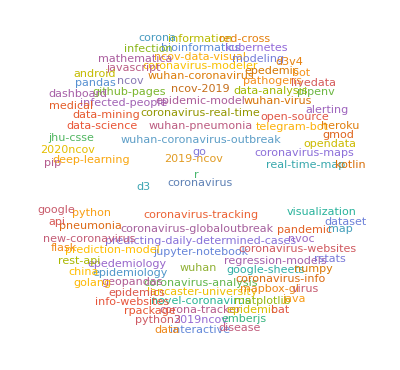

```mathematica
WordCloud[%]
```

```mathematica
Export["D:\\git\\wolfram-coronavirus\\images\\github-topic-wordcloud.png",Out[113]]
```

D:\git\wolfram-coronavirus\images\github-topic-wordcloud.png

```mathematica
Length[json["items"]]
```

```mathematica
items=json["items"];
```

```mathematica
Table[gettags[json,i],{i,30}]//Dataset
```

```mathematica
Keys[json]
```

```mathematica
json["incomplete_results"]
```

```mathematica
json["items"]//Length
```

```mathematica
json
```